```mathematica
Remove["Global`*"]
Γself[a_,b_,c_]:=Subscript[Γ, " "b.c]^a(*Γself表面Γ这个符号*)
zuobiao={x,y}(*待输入*);
g0={(2/(1-(x^2+y^2)))^2,(2/(1-(x^2+y^2)))^2};
g=DiagonalMatrix[g0];(*待输入*)
dimg=Dimensions[g][[1]];
ing=Inverse[g];


(*Γ的计算*)
cΓself[a_,b_,c_]:=Block[{μ=Position[zuobiao,a][[1,1]],ν=Position[zuobiao,b][[1,1]],σ=Position[zuobiao,c][[1,1]],k},
Simplify[Sum[(1/2)*ing[[μ,k]]*(D[g[[ν,k]],c]+D[g[[σ,k]],b]-D[g[[σ,ν]],zuobiao[[k]]]),{k,dimg}]]]
Table[Γself[μ,ν,σ]==cΓself[μ,ν,σ],{μ,zuobiao},{ν,zuobiao},{σ,zuobiao}]//TableForm(*列表*)


(*给出测地线方程，带参数λ*)
cedixian=Table[zuobiao[[k]]''==-Sum[cΓself[zuobiao[[k]],zuobiao[[i]],zuobiao[[j]]]*zuobiao[[i]]'*zuobiao[[j]]',{i,dimg},{j,dimg}],{k,dimg}];

cedixian=cedixian/.Join[Table[zuobiao[[k]]->zuobiao[[k]][λ],{k,dimg}],Table[zuobiao[[k]]'->zuobiao[[k]]'[λ],{k,dimg}],Table[zuobiao[[k]]''->zuobiao[[k]]''[λ],{k,dimg}]]



(*给出指数映射*)
exp[q_,u_]:=Block[{sol},sol=NDSolve[Join[cedixian,Table[zuobiao[[k]][0]==q[[k]],{k,dimg}],Table[zuobiao[[k]]'[0]==u[[k]],{k,dimg}]],Table[zuobiao[[k]],{k,dimg}],{λ,0,1}];Table[zuobiao[[k]][1],{k,dimg}]/. sol[[1]]
]

exp[{-0.5,-0.5},{0.5,0.3}]
exp[{0.2,-0.4},{-0.2,0.8}]
```

Γ_(x.x)^x==-(2 x)/(-1+x^2+y^2)
Γ_(x.y)^x==-(2 y)/(-1+x^2+y^2) | Γ_(y.x)^x==-(2 y)/(-1+x^2+y^2)
Γ_(y.y)^x==(2 x)/(-1+x^2+y^2)
Γ_(x.x)^y==(2 y)/(-1+x^2+y^2)
Γ_(x.y)^y==-(2 x)/(-1+x^2+y^2) | Γ_(y.x)^y==-(2 x)/(-1+x^2+y^2)
Γ_(y.y)^y==-(2 y)/(-1+x^2+y^2)

{x''[λ]==(2 x[λ] x'[λ]^2)/(-1+x[λ]^2+y[λ]^2)+(4 y[λ] x'[λ] y'[λ])/(-1+x[λ]^2+y[λ]^2)-(2 x[λ] y'[λ]^2)/(-1+x[λ]^2+y[λ]^2),y''[λ]==-(2 y[λ] x'[λ]^2)/(-1+x[λ]^2+y[λ]^2)+(4 x[λ] x'[λ] y'[λ])/(-1+x[λ]^2+y[λ]^2)+(2 y[λ] y'[λ]^2)/(-1+x[λ]^2+y[λ]^2)}

{0.376057,-0.297723}

{0.0776407,0.521556}

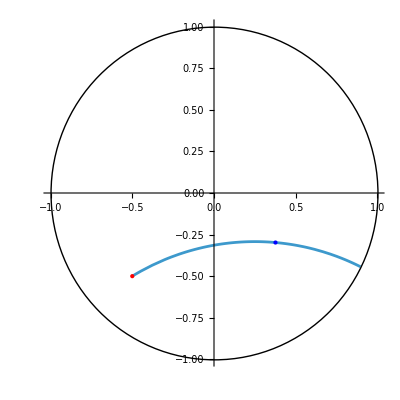

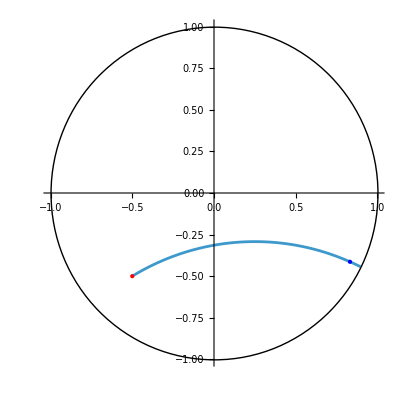

```mathematica
(*测地线绘图展示eg：（庞加莱圆盘）*)
drawGeodesic[q_,u_]:=Module[{sol},sol=NDSolve[Join[cedixian,Table[zuobiao[[k]][0]==q[[k]],{k,dimg}],Table[zuobiao[[k]]'[0]==u[[k]],{k,dimg}]],Table[zuobiao[[k]],{k,dimg}],{λ,0,5}];
ParametricPlot[Evaluate[Table[zuobiao[[k]][λ],{k,dimg}]/. sol[[1]]],{λ,0,5},PlotRange->{{-1,1},{-1,1}},Epilog->{Circle[],PointSize[Large],Red,Point[q],Blue,Point[exp[q,u]]}]]
drawGeodesic[{-0.5,-0.5},{0.5,0.3}]
drawGeodesic[{-0.5,-0.5},{1,0.6}]
```